```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\cassandra\Desktop\physics-132

```mathematica
rawData = Import["linear.tsv", HeaderLines ->1]
```

{{0.35,0.0227273,0.0660252},{0.45,0.0719697,0.0733242},{0.55,0.0757576,0.0370706},{0.65,0.104167,0.0431344},{0.75,0.138258,0.0746537},{0.85,0.17803,0.0117017},{0.95,0.179924,0.0524983},{1.05,0.24053,0.0683561},{1.15,0.25947,0.0690127},{1.25,0.291667,0.0121617},{1.35,0.293561,0.0801711},{1.45,0.36553,0.0622583},{1.55,0.359848,0.05188},{1.65,0.469697,0.0411802},{1.75,0.44697,0.0596545},{1.85,0.501894,0.0255887},{1.95,0.547348,0.0128066},{2.05,0.541667,0.0799983},{2.15,0.568182,0.0766612},{2.25,0.623106,0.0711257},{2.35,0.649621,0.0935594},{2.45,0.727273,0.0580026},{2.55,0.693182,0.0955998},{2.65,0.727273,0.0385832},{2.75,0.732955,0.0774145},{2.85,0.731061,0.0238581},{2.95,0.899621,0.0972279},{3.05,0.875,0.0174876},{3.15,0.956439,0.0694303},{3.25,1.,0.083632}}

```mathematica
a = rawData[[All,{1,2}]]
```

{{0.35,0.0227273},{0.45,0.0719697},{0.55,0.0757576},{0.65,0.104167},{0.75,0.138258},{0.85,0.17803},{0.95,0.179924},{1.05,0.24053},{1.15,0.25947},{1.25,0.291667},{1.35,0.293561},{1.45,0.36553},{1.55,0.359848},{1.65,0.469697},{1.75,0.44697},{1.85,0.501894},{1.95,0.547348},{2.05,0.541667},{2.15,0.568182},{2.25,0.623106},{2.35,0.649621},{2.45,0.727273},{2.55,0.693182},{2.65,0.727273},{2.75,0.732955},{2.85,0.731061},{2.95,0.899621},{3.05,0.875},{3.15,0.956439},{3.25,1.}}

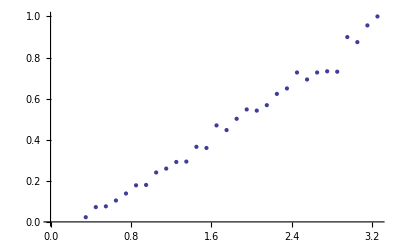

```mathematica
ListPlot[a]
```

```mathematica
line1 = Fit[a,{1,x},x]
```

-0.105631+0.322994 x

```mathematica
FindFit[a, m*x+b, {m,b},x]
```

{m→0.322994,b→-0.105631}

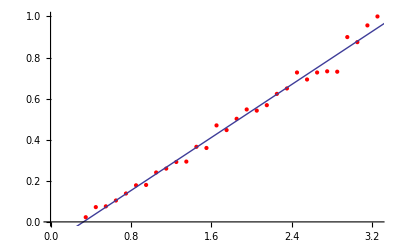

```mathematica
Show[ListPlot[a,PlotStyle->Red],Plot[m x+b/.{m->0.3229935618700913,b->-0.10563083560858849},{x,0,30}]]
```

```mathematica
errors = rawData[[All,3]]
```

{0.0660252,0.0733242,0.0370706,0.0431344,0.0746537,0.0117017,0.0524983,0.0683561,0.0690127,0.0121617,0.0801711,0.0622583,0.05188,0.0411802,0.0596545,0.0255887,0.0128066,0.0799983,0.0766612,0.0711257,0.0935594,0.0580026,0.0955998,0.0385832,0.0774145,0.0238581,0.0972279,0.0174876,0.0694303,0.083632}

```mathematica
Show[ListPlot[a,PlotStyle->Red], Plot[line1,{x,0,30}]]
```

-Graphics-

```mathematica
LinearModelFit[a,x,x]
```

FittedModel[-0.105631+0.322994 x]

```mathematica
Dominic Martinez-Ta
```